```mathematica
CellPrint[Cell["Directory","Section"]]
CellPrint[Cell["Main code & XZ independent noise:","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"general_codes.nb"],Appearance->"DialogBox"]
CellPrint[Cell["DATA & code definitions :","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"data_summary.nb"],Appearance->"DialogBox"]
CellPrint[Cell["Depoloarizing Noise:","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"depolarizing_noise.nb"],Appearance->"DialogBox"]
CellPrint[Cell["XZ uneven Noise:","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"xz_uneven_noise.nb"],Appearance->"DialogBox"]
CellPrint[Cell["Approxiating polynomials:","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"approximating_polynomials.nb"],Appearance->"DialogBox"]
CellPrint[Cell["Depolarizing noise with Measurement error :","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"depolarizing_noise_ME.nb"],Appearance->"DialogBox"]
CellPrint[Cell["XZ (symmetric) noise with Measurement error :","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"xz_noise_ME.nb"],Appearance->"DialogBox"]
CellPrint[Cell["XZ uneven noise with Measurement error :","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"xz_uneven_noise_ME.nb"],Appearance->"DialogBox"]
SetDirectory[NotebookDirectory[]]
```

## Directory

Main code & XZ independent noise:

DATA & code definitions :

Depoloarizing Noise:

XZ uneven Noise:

Approxiating polynomials:

Depolarizing noise with Measurement error :

XZ (symmetric) noise with Measurement error :

XZ uneven noise with Measurement error :

/Users/naomi/Dropbox/&Projects/Small codes

## Analysis Code

```mathematica
(*  computeMEq[] - defined in xz_noise_ME   *)
(* syndromeDistances[] - defined in xz_noise_ME *)
(* encodingPowerArray[] - defined in xz_noise_ME *)
(* encodingPowerPQArray[] - defined in xz_noise_ME *)

computePolyMatrixDepol[results_,nQ_,pVal_]:=Module[{polynomials},
polynomials = polynomialDepol[results,nQ];
polynomials=(Plus@@#&/@#)&/@polynomials;
polynomials/.{p->pVal}
]

computeFMatDepol[syndromes_,polynomials_,nQ_,p_]:=Module[{fMatrix},
fMatrix=computePolyMatrixDepol[polynomials,nQ,p];

If[Plus@@Flatten@fMatrix≠1,Print[{"ERROR: fMatrix doesn't sum to 1. Check the number of qubits is correctly defined",Plus@@Flatten@fMatrix}]];
fMatrix
]

computeMEsuccessRateDepol[syndromes_,polynomials_,nQ_,p_,qRange_,precomputedDistance_:None]:=
Module[{fMatrix,distances,nS,nStabs,fVec},
nStabs=Length[syndromes[[1]]];
nS=Length[syndromes];
fMatrix=computeFMatDepol[syndromes,polynomials,nQ,p];
fVec=Max[#]&/@fMatrix;

distances = syndromeDistances[syndromes,nS];
computeMEq[fMatrix,distances,#,nS,nStabs]&/@qRange
(*computeMEq2[fVec,distances,#,nS,nStabs]&/@qRange*)
]

successRateArrayDepol[syndromes_,poly_,nQ_,pRange_,qRange_]:=Module[{qR,pR,test},
pR = Table[p,{p,pRange[[1]],pRange[[2]],pRange[[3]]}];
qR=Table[q,{q,qRange[[1]],qRange[[2]],qRange[[3]]}];

test=Table[computeMEsuccessRateDepol[syndromes,poly,nQ,p,qR],{p,pRange[[1]],pRange[[2]],pRange[[3]]}];

ArrayFlatten[Table[{pR[[i]],qR[[j]],test[[i,j]]},{i,1,Length[pR]},{j,1,Length[qR]}],1]
]
```

```mathematica
CellPrint[Cell["DATA :","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"data_summary.nb"],Appearance->"DialogBox"]
```

DATA :

```mathematica
{syndromesDepolP5,polyDepolP5} =<<"data/planarDepol5.txt";
{syndromesDepolP6,polyDepolP6}=<<"data/planarDepol6.txt";
{syndromesDepolP7a,polyDepolP7a}=<<"data/planarDepol7a.txt";
{syndromesDepolP7b,polyDepolP7b}=<<"data/planarDepol7b.txt";
{syndromesDepolP8,polyDepolP8}=<<"data/planarDepol8.txt";
{syndromeDepolP9,polyDepolP9}=<<"data/planarDepol9.txt";
```

## Generate data

Evaluates data and stores to file. Cells are marked as deployed after the results have been evaluated to avoid files being overwritten.

### 5 qubit planar (for testing...)

```mathematica
successRateArrayDepol[syndromesDepolP5,polyDepolP5,5,{0.001,0.2,0.01},{0,0.01,0.001}]>>"data/MEdepolP5"
```

### 7 qubit planar

```mathematica
successRateArrayDepol[syndromesDepolP7a,polyDepolP7a,7,{0.001,0.12,0.001},{0,0.003,0.003}]>>"data/MEdepolP7"
```

### 8 qubit planar

```mathematica
successRateArrayDepol[syndromesDepolP8,polyDepolP8,8,{0.001,0.1,0.0025},{0,0.0022,0.0001}]>>"data/MEdepolP8"
```

### 9 qubit planar

```mathematica
successRateArrayDepol[syndromeDepolP9,polyDepolP9,9,{0.001,0.11,0.005},{0,0.0037,0.0003}]>>"data/MEdepolP9"
```

### 13 qubit planar

### 7 qubit color code

```mathematica
successRateArrayDepol[syndromeDepolC7,polyDepolC7,7,{0.001,0.11,0.005},{0,0.004,0.0002}]>>"data/MEdepolC7"
```

### 11 qubit color code

```mathematica
successRateArrayDepol[syndromeDepolC11,truncatePolynomials[polyDepolC11,5],11,{0.001,0.2,0.02},{0,0.004,0.0003}]>>"data/MEdepolC11"
```

{ERROR: fMatrix doesn't sum to 1. Check the number of qubits is correctly defined,1.}

{ERROR: fMatrix doesn't sum to 1. Check the number of qubits is correctly defined,0.999998}

{ERROR: fMatrix doesn't sum to 1. Check the number of qubits is correctly defined,0.999982}

{ERROR: fMatrix doesn't sum to 1. Check the number of qubits is correctly defined,0.999909}

{ERROR: fMatrix doesn't sum to 1. Check the number of qubits is correctly defined,0.999688}

{ERROR: fMatrix doesn't sum to 1. Check the number of qubits is correctly defined,0.999159}

{ERROR: fMatrix doesn't sum to 1. Check the number of qubits is correctly defined,0.998086}

{ERROR: fMatrix doesn't sum to 1. Check the number of qubits is correctly defined,0.996149}

{ERROR: fMatrix doesn't sum to 1. Check the number of qubits is correctly defined,0.992957}

### 15 qubit gauge color code

```mathematica
pGCCDepol[p_]:=Module[{noError,e1,x1z1},
noError=(1-p)^15;
e1=15*(1-p)^14*p;
x1z1=15*14*(1-p)^13*(p/3)^2;
noError+e1+x1z1
]
qGCC[q_]:=Module[{noError,e1,e2},
noError=(1-q)^18;
e1=18*(1-q)^17*q; (* 1 error in each channel*)
e2=(36+54+3)(1-q)^16*q^2;(* 2 measurement errors on different stabilizers  *)
(noError +e1+e2)^2
]

ArrayFlatten[Table[{p,q,pGCCDepol[p]qGCC[q]},{p,0,0.05,0.0002},{q,0,0.02,0.0005}],1]>> "data/MEdepolGCC15";
```

## Plot results

```mathematica
planar8MEdata=<<"data/planar8MEdata";
planar9MEdata=<<"data/planar9MEdata";
planar13MEdata=<<"data/planar13MEdata";
```

```mathematica
plotParams={thickness->0.01};
```

### 5 qubit planar code

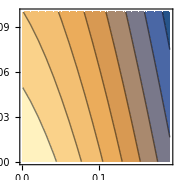

```mathematica
test =<<"data/MEdepolP5";
ListContourPlot[encodingPowerArray[test]]
```

### 7 qubit planar code

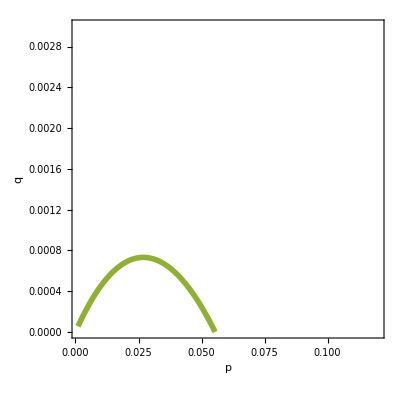
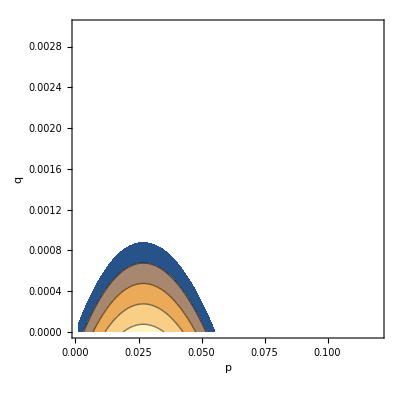

```mathematica
MEdepolP7=<<"data/MEdepolP7";
{plotDepolME7,plotDepolME72}={
ListContourPlot[encodingPowerArray[MEdepolP7],PlotRange->{0,2},FrameLabel->{"p","q"},ContourShading->None,Contours->1,ContourStyle->Directive[Opacity[1],Thickness[thickness/.plotParams],ColorData[97,3]]],ListContourPlot[encodingPowerPQArray[MEdepolP7],PlotRange->{1,1.01},FrameLabel->{"p","q"}]}
```

### 8 qubit planar code

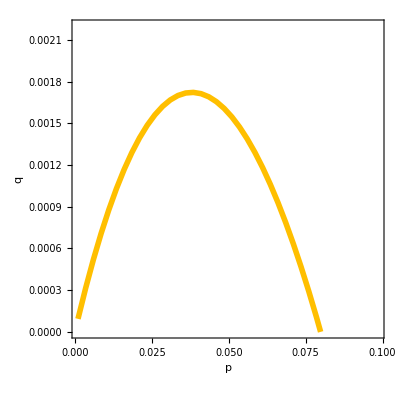
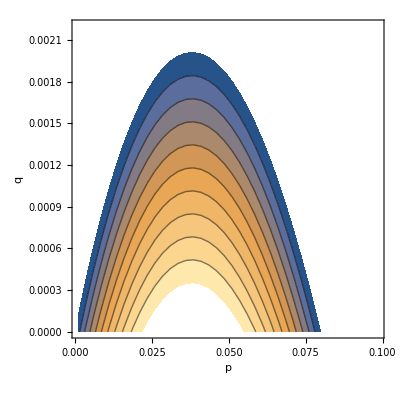

```mathematica
MEdepolP8=<<"data/MEdepolP8";
{plotDepolME8,plotDepolME82}={
ListContourPlot[encodingPowerArray[MEdepolP8],PlotRange->{0,2},FrameLabel->{"p","q"},ContourShading->None,Contours->1,ContourStyle->Directive[Opacity[1],Thickness[thickness/.plotParams],ColorData[97,8]]],ListContourPlot[encodingPowerPQArray[MEdepolP8],PlotRange->{1,1.01},FrameLabel->{"p","q"}]}
```

### 9 qubit planar code

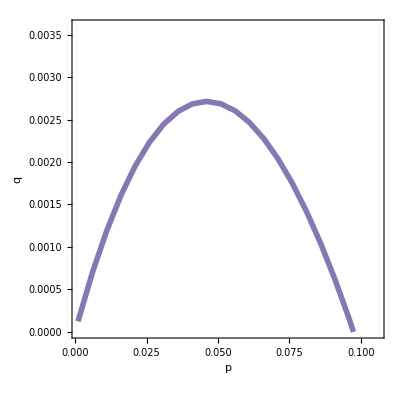
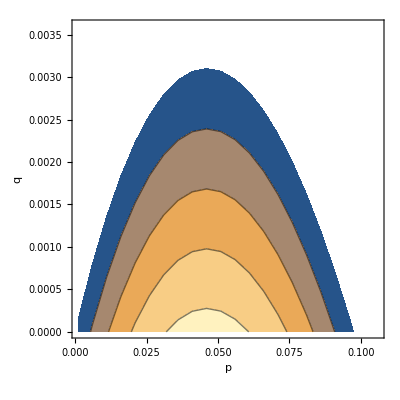

```mathematica
MEdepolP9=<<"data/MEdepolP9";
{plotDepolME9,plotDepolME92}={
ListContourPlot[encodingPowerArray[MEdepolP9],PlotRange->{0,2},FrameLabel->{"p","q"},ContourShading->None,Contours->1,ContourStyle->Directive[Opacity[1],Thickness[thickness/.plotParams],ColorData[97,5]]],ListContourPlot[encodingPowerPQArray[MEdepolP9],PlotRange->{1,1.05},FrameLabel->{"p","q"}]}
```

### 13 qubit planar code

### 7 qubit color code

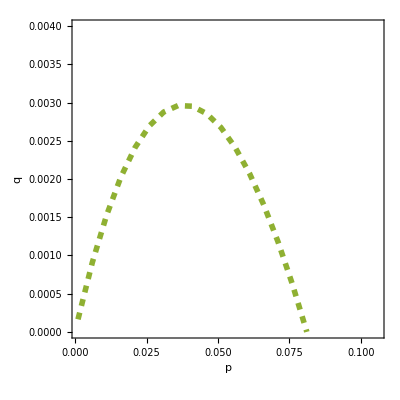
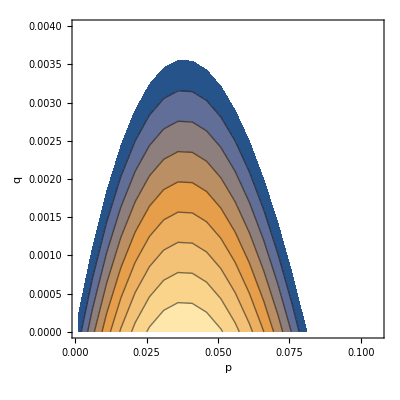

```mathematica
MEdepolC7=<<"data/MEdepolC7";
{plotDepolMEC7,plotDepolMEC72}={
ListContourPlot[encodingPowerArray[MEdepolC7],PlotRange->{0,2},FrameLabel->{"p","q"},ContourShading->None,Contours->1,ContourStyle->Directive[Opacity[1],Thickness[thickness/.plotParams],Dashed,ColorData[97,3]]],ListContourPlot[encodingPowerPQArray[MEdepolC7],PlotRange->{1,1.02},FrameLabel->{"p","q"}]}
```

### 11 qubit color code

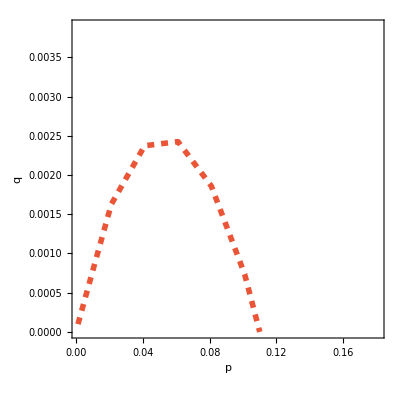
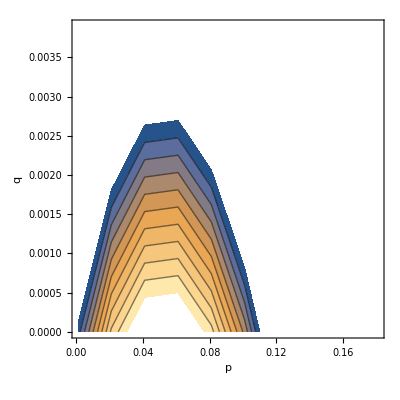

```mathematica
MEdepolC11=<<"data/MEdepolC11";
{plotDepolMEC11,plotDepolMEC112}={
ListContourPlot[encodingPowerArray[MEdepolC11],PlotRange->{0.5,1.5},FrameLabel->{"p","q"},ContourShading->None,Contours->1,ContourStyle->Directive[Opacity[1],Thickness[thickness/.plotParams],Dashed,ColorData[97,11]]],ListContourPlot[encodingPowerPQArray[MEdepolC11],PlotRange->{1,1.02},FrameLabel->{"p","q"}]}
```

## Summary plots

```mathematica
MEdepolP7=<<"data/MEdepolP7";
MEdepolP8=<<"data/MEdepolP8";
MEdepolP9=<<"data/MEdepolP9";
MEdepolC7=<<"data/MEdepolC7";
MEdepolC11=<<"data/MEdepolC11";
MEdepolGCC15=<<"data/MEdepolGCC15";
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

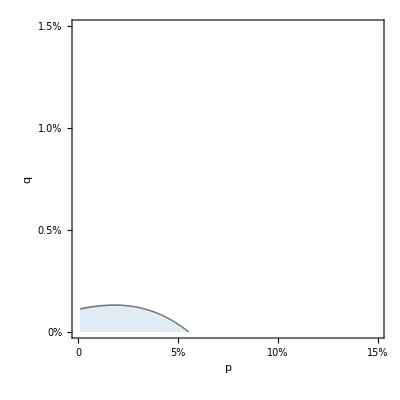
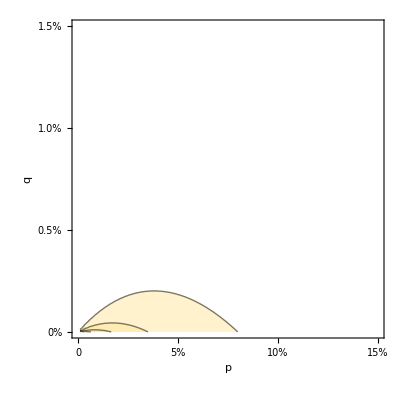
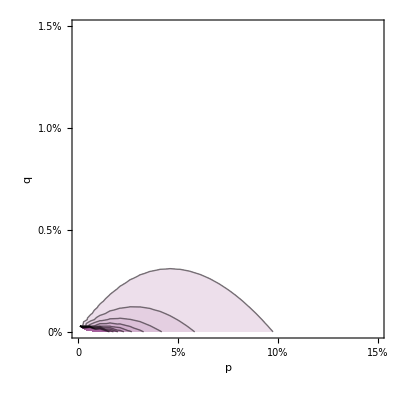
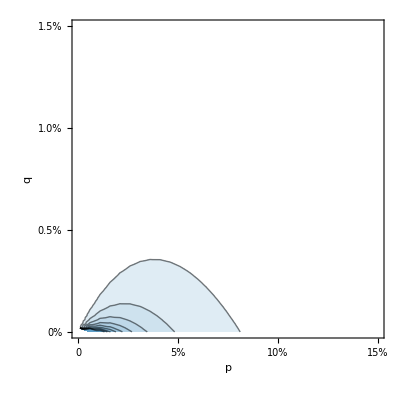
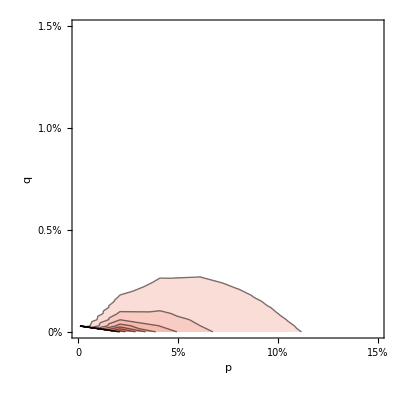
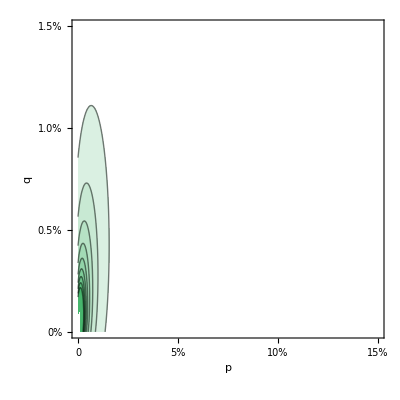

```mathematica
cp1[data_,col_]:=ListContourPlot[correctingPowerArray[data],
PlotRange->{{0,0.15},{0,0.015},{0.9999,10}},
FrameLabel->{"p","q"},
LabelStyle->20,
Contours->Range[10]*0.5,
ContourShading->Table[Blend[{White,ColorData[97,col]},x],{x,0,1,1/10}],FrameTicks->{{0,{0.05,"5%"},{0.1,"10%"},{0.15,"15%"}},{{0,"0%"},{0.005,"0.5%"},{0.01,"1.0%"},{0.015,"1.5%"}},{},{}}]

p1=cp1[#[[1]],#[[2]]]&/@{{MEdepolP7,7},{MEdepolP8,8},{MEdepolP9,9},{MEdepolC7,7},{MEdepolC11,11},{MEdepolGCC15,15}}
```

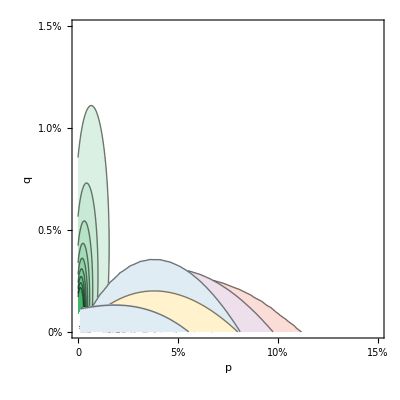

```mathematica
Show[p1[[6]],p1[[5]],p1[[3]],p1[[4]],p1[[2]],p1[[1]]]
```

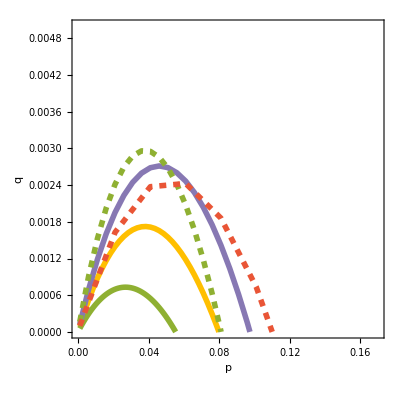

```mathematica
Show[plotDepolME8,plotDepolME7,plotDepolME9,plotDepolMEC7,plotDepolMEC11,PlotRange->{{0,0.17},{0,0.005}},LabelStyle->20]
```